```mathematica
WM=ResourceFunction["WolframModel"];
```

```mathematica
rule={{x,y}}->{{x,y},{y,z}};
init={{1,2}}
```

{{1,2}}

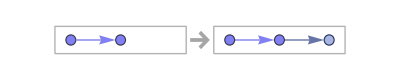

```mathematica
RulePlot[WM[rule]]
```

```mathematica
WM[rule, init, 3]
```

WolframModelEvolutionObject[…]

```mathematica
?WolframModelEvolutionObject
```

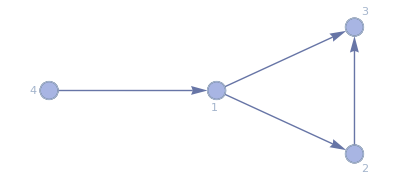

```mathematica
ResourceFunction["WolframModelPlot"][{{1,2},{1,3},{2,3},{4,1}},VertexLabels->Automatic]
```

```mathematica
ResourceFunction["WolframModelPlot"][#,VertexLabels->Automatic]&/@ResourceFunction["WolframModel"][{{{x,y}}->{{x,y},{y,z}}},{{1,2}},2,"StatesList"]
```

```mathematica
rule
```

{{x,y}}→{{x,y},{y,z}}

```mathematica
WMPlot=ResourceFunction["WolframModelPlot"]
```

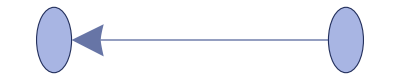
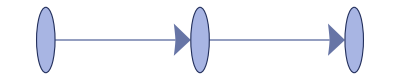
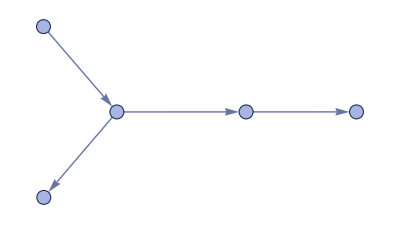

```mathematica
WMPlot/@WM[rule, {{1,2}}, 2, "StatesList"]
```

```mathematica
Graph[Rule@@@#,VertexLabels->Automatic,VertexStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph","VertexStyle"],EdgeStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph","EdgeLineStyle"],GraphLayout->"LayeredDigraphEmbedding"]&/@ResourceFunction["WolframModel"][{{{x,y}}->{{x,y},{y,z}}},{{1,2}},4,"StatesList"]
```

```mathematica
@@@
```

```mathematica
GraphPlot[ResourceFunction["MultiwaySystem"][{"AB"->"BAB","BA"->"A"},"ABA",4,"EvolutionEventsGraph","IncludeInitializationEvents"->False,"IncludeStepNumber"->True],GraphLayout->{"LayeredDigraphEmbedding"}]
```

-Graphics-

```mathematica
GraphPlot[ResourceFunction["MultiwaySystem"][{"AB"->"BAB","BA"->"A"},"ABA",4,"StatesGraph","IncludeInitializationEvents"->False,"IncludeStepNumber"->True],GraphLayout->{"LayeredDigraphEmbedding"}]
```

-Graphics-

```mathematica
statesGraph = ResourceFunction["MultiwaySystem"][{"AB"->"BAB","BA"->"A"},"ABA",4,"StatesGraph"]
```

-Graphics-

```mathematica
causalGraph=ResourceFunction["MultiwaySystem"][{"AB"->"BAB","BA"->"A"},"ABA",4,"CausalGraph"]
```

-Graphics-

```mathematica
DualPlanarGraph[statesGraph]
```

-Graphics-